```mathematica
ToBaseWord[w_]:=Block[{wn},wn=WordData[w];If[Length[wn]≤0,w,wn[[1,1]]]];
WordHasMeaningQ[w_]:=Block[{wn},wn=WordData[w,"PartsOfSpeech"];
NumberQ[w]
||(Not[MemberQ[wn,"Preposition"]]
&&Not[MemberQ[wn,"Conjunction"]]
&&Not[MemberQ[wn,"Determiner"]]
)
];
YearExpenseData[year_]:=Block[{expensesXml,accountInfo,dict,wordToAccountIds,sum,maxCount,maxAmount,json},
expensesXml=Import["http://www.whatwepayfor.com/api/getBudgetAccount?income=100&showChange=1&showExtra=1&year="<>ToString[year],"XML"];
accountInfo=SortBy[
ReleaseHold[{"account",Hold[ToExpression["amounti"]],"function","subfunction"}/.Cases[expensesXml,XMLElement["item",__,__],Infinity][[All,2]]],
(-#[[2]])&];
dict=Union[accountInfo[[All,3]],accountInfo[[All,4]]];
wordToAccountIds=Select[{#[[1,1]],#[[All,2]]}&/@GatherBy[
Flatten[Function[{accountIndex},{ToBaseWord[ToLowerCase[#]],accountIndex}&/@StringSplit[accountInfo[[accountIndex,1]],RegularExpression["[^a-zA-Z0-9]+"]]]/@
Range[1,Length[accountInfo]],1],
#[[1]]&],
WordHasMeaningQ[#[[1]]]&];
Export["/home/xcolwell/words_"<>ToString[year]<>".txt",StringJoin[Riffle[ToString/@wordToAccountIds[[All,1]]," "]]];
sum=SortBy[
Block[{w,ids},{w,ids}={#[[1]],Union[#[[2]]]};{w,Length[ids],Total[accountInfo[[ids,2]]],ids}]&/@wordToAccountIds,
{-#[[2]],#[[1]]}&];
maxCount=Max[Abs[sum[[All,2]]]];
maxAmount=Max[Abs[sum[[All,3]]]];
json="{\"summary\":["<>ToString[maxCount]<>","<>ToString[maxAmount]<>"],\n"<>
(* Sorted in descending order by count *)
"\"yed\":"<>
StringReplace[
ToString[sum,InputForm],
{"{"->"[","}"->"]"}]<>",\n"<>

"\"dict\":"<>
StringReplace[
ToString[dict,InputForm],
{"{"->"[","}"->"]"}]<>",\n"<>

"\"functions\":"<>
StringReplace[ToString[
accountInfo[[All,3;;4]]/.((#[[1]]->#[[2]])&/@Partition[Riffle[dict,Range[1,Length[dict]]],2]),
InputForm],
{"{"->"[","}"->"]"}]<>",\n"<>
(* Sorted in descending order by amount *)
"\"accounts\":"<>
StringReplace[ToString[accountInfo[[All,1;;2]],InputForm],
{"{"->"[","}"->"]"}]<>"}";
Export["/home/xcolwell/yed_"<>ToString[year]<>".json",json,"Text"];
PrintTemporary[year];
sum
];
```

```mathematica
sums=YearExpenseData/@Range[1984,2010];
```

```mathematica
sums[[1,All,{1,2,3}]]
```

{{fund,267,261824126},{expense,152,16718672},{salary,128,10468011},{interest,102,108400344},{trust,94,276248976},{funds,74,27756881},{program,72,51238247},{national,65,15084902},{payment,60,36087419},{contribution,56,-30612688},{loan,54,-23256855},{service,53,10729102},{gift,51,-9019},{account,47,30544256},{investment,46,-1137757},{miscellaneous,46,512023},{general,45,-17151095},{deposit,43,-17389584},{federal,40,213980082},{public,39,3209094},{research,39,36369248},{development,38,38539563},{state,38,43984786},{foreign,37,4665352},{administration,35,1699053},{services,34,25582672},{insurance,33,261300780},{receipts,33,-4980966},{land,32,-6516924},{assistance,31,25955788},{military,30,51764746},{fee,29,-259650},{office,29,563539},{retirement,29,5832110},{construction,28,7464047},{special,28,2868216},{army,27,62129326},{maintenance,27,72743139},{air,26,86132921},{disability,26,26042566},{force,26,84194359},{grant,26,33620230},{operation,26,73720650},{housing,25,23677744},{international,25,9609918},{navy,24,75049325},{security,24,170666866},{advance,23,-16142804},{facility,23,2774401},{management,22,2441980},{indian,21,1336323},{liquidate,21,27716051},{benefit,20,8774981},{contribute,20,52525},{education,20,5849409},{sale,20,-2232726},{commission,19,-167835},{agency,17,-4584846},{forest,17,869812},{not,17,-671474},{operations,17,5514585},{sales,17,-1319316},{unemployment,17,21706778},{classified,16,-636392},{defense,16,34094540},{donation,16,-6646},{power,16,134602},{recovery,16,-468490},{rural,16,12457317},{s,16,-8492},{building,15,316662},{energy,15,11156729},{operating,15,5757598},{property,15,-166034},{railroad,15,2080782},{activity,14,10924049},{conservation,14,2231076},{currency,14,-84033},{debt,14,153072847},{reserve,14,5778763},{science,14,809763},{united,14,6899601},{bank,13,-11492418},{permanent,13,567379},{procurement,13,74500376},{profits,13,-1095570},{project,13,585582},{resource,13,2423719},{river,13,270655},{appropriation,12,516412},{civil,12,5775485},{corps,12,8987020},{health,12,27108717},{improvement,12,1637731},{pension,12,14017638},{proprietary,12,-844486},{reclamation,12,-576073},{survivor,12,160531249},{annuity,11,-1647},{bequest,11,-1386},{rail,11,53137},{rent,11,-2301821},{american,10,189198},{compensation,10,6282212},{corporation,10,1066652},{departmental,10,564124},{government,10,6113519},{highway,10,14117616},{income,10,12274016},{library,10,330132},{personnel,10,48362753},{acquisition,9,1005196},{act,9,-234999},{charge,9,-202598},{congress,9,132925},{fhi,9,-5656875},{home,9,1837968},{industry,9,89789},{related,9,2001467},{repayment,9,-7864025},{revenue,9,-856339},{senate,9,72980},{u,9,-79927},{administrative,8,30084},{control,8,4358106},{cooperative,8,-169630},{court,8,207399},{credit,8,8499014},{department,8,177882},{guarantee,8,-14910},{guard,8,5820610},{hospital,8,42568066},{institute,8,4593196},{revolve,8,469238},{technical,8,942949},{tribal,8,2058513},{water,8,49102},{agricultural,7,9184806},{aid,7,15146014},{district,7,422692},{earnings,7,-38098},{economic,7,3735154},{endowment,7,320341},{family,7,16020650},{fdi,7,-2126159},{flood,7,298333},{marine,7,8880610},{naval,7,254768},{park,7,607966},{post,7,8621},{product,7,-101860},{royalty,7,-3610679},{safety,7,304104},{substance,7,1226626},{system,7,1609073},{technology,7,239227},{timber,7,-190472},{training,7,7399474},{transfer,7,-601935},{use,7,-36982},{veteran,7,-26468},{wildlife,7,62421},{airport,6,1458196},{area,6,458130},{capital,6,408105},{center,6,26284},{child,6,16026137},{commodity,6,-1191422},{community,6,3999102},{conditional,6,-3603},{disposal,6,-86039},{dot,6,-7017},{electric,6,-240145},{emergency,6,-115712},{fishing,6,13004},{foundation,6,20225},{inter,6,-1751091},{lease,6,372873},{liability,6,1193286},{medical,6,29011150},{or,6,-6392770},{personal,6,-172088},{phs,6,-582},{postal,6,-197788},{president,6,26310},{real,6,-119646},{received,6,-5827314},{rehabilitation,6,1480760},{repayable,6,-4909595},{secretary,6,-42360},{supplemental,6,21637157},{tax,6,-13307},{transportation,6,-43839},{wide,6,10683097},{aircraft,5,34727555},{allowance,5,17381},{bureau,5,36786},{cancelled,5,-18783},{colorado,5,-32353},{dam,5,-13050},{employee,5,1544665},{employer,5,-19853000},{employment,5,6941996},{enforcement,5,10261651},{equipment,5,899805},{evaluation,5,26863596},{exchange,5,85383},{foasi,5,-13686537},{fsmi,5,-22525541},{h,5,-397930},{hazardous,5,378611},{information,5,564792},{inspection,5,-57351},{inspector,5,212549},{intragovernmental,5,-18783},{member,5,44958},{memorial,5,1861},{museum,5,115754},{oil,5,-1336054},{outer,5,-6711355},{premium,5,-5383859},{preservation,5,-104434},{receivables,5,-18783},{recreation,5,-20605},{regional,5,120948},{road,5,-10471},{shelf,5,-6711355},{stock,5,2653945},{superfund,5,378611},{surplus,5,-160609},{test,5,26863596},{transmission,5,-170277},{undistributed,5,-18783},{visitor,5,-1350},{washington,5,247089},{academy,4,-1754},{advancement,4,89949},{airway,4,1461107},{alaska,4,-9828},{arts,4,166765},{authority,4,830571},{black,4,281345},{blind,4,40099},{blm,4,-7273},{board,4,-600532},{boulder,4,-13024},{broadcasting,4,308206},{business,4,406872},{c,4,-2},{canal,4,7771},{canyon,4,-13024},{capitol,4,41455},{care,4,18715476},{collected,4,-4944065},{collection,4,2700559},{columbia,4,425217},{committee,4,7657},{congressional,4,127012},{continental,4,-6561355},{copyright,4,102330},{counsel,4,21555},{credits,4,-132243},{educational,4,98527},{etc,4,-2961},{fica,4,-3350000},{fiscal,4,4631958},{fisherman,4,2215},{fishery,4,-11685},{gas,4,-1574813},{grazing,4,-11054},{house,4,51670},{interior,4,-7395},{investigation,4,1586488},{joint,4,7657},{lung,4,281345},{material,4,-77150},{mineral,4,689035},{monetary,4,6921913},{nuclear,4,-27486},{nutrition,4,17561654},{organization,4,881679},{patient,4,-197},{pay,4,16724872},{petroleum,4,1517160},{port,4,-53751},{printing,4,105876},{purchase,4,-229568},{range,4,1468},{reduction,4,-21950},{refund,4,1302809},{supply,4,4508636},{telephone,4,2427436},{unconditional,4,-1128},{abuse,3,848017},{acquired,3,-7042},{affairs,3,-66227},{african,3,70987},{age,3,160537169},{agriculture,3,1430889},{amended,3,-215211},{appalachian,3,157600},{archives,3,0},{armed,3,24262},{arms,3,53061},{basin,3,567},{california,3,-18606},{claim,3,237260},{costs,3,16534301},{d,3,-69209},{damaged,3,-19404},{deepwater,3,488},{dollar,3,-488797},{drug,3,90182},{employ,3,-39807},{enterprise,3,40727},{environmental,3,599675},{era,3,8924},{farm,3,-69301},{feed,3,-22301},{fha,3,65393},{financing,3,-10307794},{forfeiture,3,-160},{grading,3,-69301},{grassland,3,-42134},{grounds,3,93820},{guaranty,3,288},{handicapped,3,241438},{harbor,3,1},{higher,3,376559},{humanities,3,140118},{hunting,3,-1589},{i,3,-354},{int,3,-163903},{interstate,3,295685},{irrigation,3,-43882},{judge,3,67},{judicial,3,2303},{legal,3,445182},{local,3,4566700},{lost,3,-19404},{low,3,3346179},{metropolitan,3,247089},{mil,3,-20401},{minority,3,53352},{nat,3,-178765},{natural,3,-694313},{normalize,3,-946736},{nsli,3,-1248781},{officer,3,282074},{old,3,160537169},{peace,3,117000},{permit,3,-1589},{planning,3,41052},{private,3,-149240},{proceeds,3,-1617002},{protection,3,1311437},{purchaser,3,-50046},{race,3,-51},{regulatory,3,36348},{reservation,3,-1589},{restoration,3,294490},{settlement,3,44622},{social,3,11673181},{southwestern,3,-55137},{space,3,4050654},{st,3,-731},{support,3,12251443},{taxis,3,-1939000},{tennessee,3,580571},{territory,3,261123},{transit,3,1795400},{treasury,3,143068336},{usgli,3,-23279},{usia,3,-3216},{valley,3,580571},{vietnam,3,8924},{waste,3,-14180},{work,3,-436},{zone,3,13356},{abandoned,2,278000},{advisory,2,-265},{alternative,2,412540},{annual,2,10082325},{annuitant,2,1472484},{aphis,2,-4094},{appeal,2,8372},{assisted,2,10082325},{bay,2,-4916},{binding,2,100000},{biological,2,0},{bonneville,2,226250},{bonus,2,-2648095},{borrowing,2,-1882515},{budget,2,255},{carrier,2,54286},{central,2,467455},{civ,2,-164},{coal,2,1066343},{coastal,2,23356},{coinage,2,-40836},{college,2,-49363},{communications,2,3921272},{consular,2,1149928},{contingency,2,10837},{conversion,2,11374664},{coo,2,-4916},{cooperation,2,5560},{council,2,1472},{county,2,-1606},{cultural,2,97924},{customs,2,1253959},{data,2,3908231},{deceased,2,355},{delaware,2,-154},{devise,2,0},{diplomatic,2,1149928},{disabled,2,623978},{disaster,2,50372},{disease,2,380489},{dod,2,21392},{doorkeeper,2,34433},{elderly,2,206339},{election,2,-15710},{electrification,2,423022},{engineer,2,-10590},{enrichment,2,381988},{exceed,2,1193101},{expansion,2,3071},{exploration,2,-30747},{export,2,827033},{f,2,-323825},{fire,2,3239},{fish,2,-3815},{fm,2,-5024},{food,2,109175},{forestry,2,73079},{friendship,2,56},{fuel,2,425105},{function,2,-987508},{hall,2,496},{harry,2,0},{heir,2,355},{historic,2,26497},{history,2,-59},{holmes,2,0},{human,2,129800},{ibwc,2,11448},{import,2,827033},{impute,2,0},{indemnity,2,9200},{intelligence,2,103767},{internal,2,1671507},{island,2,114082},{japan,2,56},{law,2,1418200},{leased,2,-537},{life,2,1272060},{m,2,-1087120},{major,2,412382},{majority,2,62},{maritime,2,-189},{mental,2,848015},{mileage,2,270},{mining,2,-1757},{mint,2,-525},{missile,2,10634738},{mutual,2,71940},{nation,2,-132677},{north,2,49975},{nps,2,-7},{official,2,85737},{offshore,2,159803},{olive,2,0},{opportunity,2,271760},{oregon,2,-18506},{overseas,2,4033},{panama,2,7771},{papago,2,0},{passenger,2,1938233},{peacekeeping,2,111600},{pershing,2,496},{policy,2,55700},{pollution,2,-29},{prevention,2,195202},{production,2,409572},{profit,2,-40836},{promote,2,9976},{promotion,2,919},{quality,2,650},{quota,2,4762874},{reconstruction,2,73732},{record,2,-59},{refuge,2,5760},{refugee,2,877411},{regulation,2,102995},{reimbursement,2,197846},{relations,2,32065},{reorganization,2,-36652},{representative,2,13799},{result,2,-20377},{retired,2,16826800},{retiree,2,-20261},{roads,2,-6025},{salvage,2,-99996},{scholarship,2,0},{scientific,2,119753},{section,2,359411},{sector,2,-209819},{sergeant,2,34433},{ship,2,-12595},{small,2,-9818},{southeastern,2,-52435},{statement,2,12},{statistics,2,54206},{storage,2,-3416},{student,2,4045640},{study,2,0},{supplementary,2,20376754},{survey,2,401966},{taxpayer,2,2057328},{telecommunication,2,404997},{trade,2,28249},{traffic,2,148074},{tres,2,-20377},{truman,2,0},{uninsured,2,-1141082},{university,2,212200},{uranium,2,381988},{urban,2,452000},{utility,2,-183933},{va,2,-169},{vessel,2,8791},{wagon,2,-4916},{watershed,2,219494},{weapon,2,8470698},{wendell,2,0},{western,2,195130},{widow,2,355},{yellowstone,2,-565},{16,1,3},{1974,1,-259568},{1993,1,786},{209,1,-423},{23,1,-40},{25,1,-35},{3,1,-40},{32,1,355947},{4,1,-40},{4601,1,3},{480,1,1377000},{6a,1,3},{75,1,-5223},{abraham,1,-8},{abroad,1,30000},{academic,1,19846},{accelerate,1,3488250},{accrual,1,16503000},{achievement,1,3488250},{action,1,440000},{administer,1,196427},{adminstration,1,-2},{adoption,1,685905},{adult,1,839045},{advanced,1,-6346},{aeronautics,1,-2},{africa,1,103000},{aged,1,-4463264},{agen,1,-140},{agreement,1,1683},{airman,1,-4304},{allied,1,-6505},{alteration,1,12500},{americans,1,317300},{ammunition,1,1980100},{ams,1,-69301},{animal,1,-1924},{anti,1,2500},{antitrust,1,44229},{art,1,34639},{asia,1,9900},{asian,1,113233},{assessment,1,-1},{assist,1,4566700},{associate,1,735891},{association,1,945000},{atlantic,1,50000},{atomic,1,6554875},{attendant,1,-1924},{attending,1,731},{attorney,1,387162},{avenue,1,11875},{aviation,1,27000},{award,1,-31962},{bankruptcy,1,107795},{barrow,1,13000},{basic,1,270760},{battle,1,-56},{betterment,1,4028},{bilateral,1,1683},{bird,1,20999},{birthplace,1,-8},{block,1,2700000},{boat,1,12500},{body,1,-62944},{bond,1,8910},{book,1,35099},{border,1,1247187},{botanic,1,2058},{bpa,1,-128629},{brush,1,-60290},{burial,1,128388},{buying,1,4815},{campaign,1,34770},{career,1,839045},{cattel,1,-18},{cemetery,1,3000},{census,1,78220},{ceremony,1,786},{character,1,-186},{chrysler,1,495},{citizen,1,1348},{civilian,1,-20237},{clearing,1,-38930},{close,1,1000},{closure,1,-303},{coast,1,-18},{coin,1,-36332},{combat,1,4699119},{commerce,1,-2},{commercial,1,-423},{commissioned,1,73750},{commissioner,1,42400},{communication,1,1194},{comp,1,-4822},{company,1,373373},{complete,1,-380},{conference,1,8910},{conrail,1,61000},{conscience,1,-277},{cont,1,-150000},{contingent,1,360},{cook,1,-712},{cooperate,1,-111},{corp,1,-102197},{corridor,1,100000},{counseling,1,3500},{crime,1,90182},{crop,1,160000},{cuba,1,10000},{dairy,1,1800},{damage,1,-609},{deaf,1,28000},{debenture,1,373373},{debris,1,-100},{deduction,1,-175678},{defender,1,41465},{democracy,1,18000},{denominate,1,-15376},{detention,1,51465},{develop,1,9986},{developmental,1,49000},{dhs,1,-8304},{differential,1,361634},{disarmament,1,18628},{discretionary,1,1250000},{distribution,1,2962},{distric,1,-25},{division,1,44229},{document,1,25700},{doi,1,-423},{domain,1,-12834},{domestic,1,135590},{donate,1,-402},{dual,1,420000},{due,1,-40},{earned,1,1192901},{east,1,18362},{eastern,1,900},{edgeter,1,-5},{elec,1,197862},{eligible,1,-35082},{elizabeth,1,-1},{elizabeths,1,-18},{embassy,1,210140},{employed,1,-33855},{engineering,1,263452},{english,1,169365},{ensure,1,3488250},{entrant,1,541761},{equity,1,3488250},{escrow,1,-17808},{esther,1,-18},{europe,1,544},{executive,1,1507},{extended,1,18000},{extension,1,334340},{extraction,1,-43747},{faa,1,-8720},{fair,1,4700},{falcon,1,-26},{federally,1,-7},{fema,1,-5889},{ffb,1,373373},{fighting,1,-11},{financial,1,3976860},{flight,1,3914292},{fnd,1,-150000},{forein,1,-200},{former,1,1171},{formula,1,2388592},{fort,1,-25},{fossil,1,264544},{foster,1,685905},{fra,1,-102197},{fslic,1,700000},{furnishings,1,1524},{furniture,1,1524},{future,1,26739},{g,1,-1087118},{gain,1,-15376},{gallaudet,1,56000},{gallery,1,34639},{gap,1,-423},{garden,1,2058},{gear,1,-609},{george,1,-5},{geothermal,1,8334},{gering,1,-25},{gertrude,1,-2},{good,1,6772},{goshen,1,-25},{grand,1,-35},{great,1,21315},{gross,1,153880949},{help,1,6000},{hhs,1,-1},{hist,1,-150000},{historical,1,-7},{holocaust,1,1864},{homeowner,1,376},{homestead,1,12000},{howard,1,156200},{hubbard,1,-2},{hydraulic,1,-100},{impact,1,600300},{inaugural,1,786},{incentive,1,12500},{include,1,-530},{independence,1,-7},{individual,1,-35082},{industrial,1,150000},{infant,1,1360000},{inland,1,-3100},{inquiry,1,46916},{insufficiency,1,1059},{interagency,1,90182},{interfund,1,-44000},{intergovernmental,1,-262},{interim,1,-3316},{invest,1,-4822},{item,1,9614},{jefferson,1,1},{job,1,270760},{john,1,4542},{judgment,1,235517},{juror,1,42400},{justice,1,197352},{kennedy,1,4542},{labor,1,61000},{lake,1,-712},{landsat,1,-6061},{laramie,1,-25},{late,1,-1657},{leaders,1,50},{learner,1,169365},{legislative,1,1318},{liabilities,1,-16},{licensee,1,-245},{lieu,1,105000},{limitation,1,6000},{lincoln,1,-8},{liquidation,1,1000},{liquidity,1,381155},{litigation,1,42879},{louis,1,-712},{mail,1,84144},{manufactured,1,5950},{manufacturing,1,-41360},{market,1,355947},{marketing,1,33473},{martha,1,191},{mass,1,1250000},{medicaid,1,20673708},{merchandising,1,-186},{migration,1,335650},{migratory,1,20999},{miner,1,1068000},{minnesota,1,-712},{minor,1,185378},{misc,1,-111},{mission,1,10012},{mississippi,1,302480},{money,1,-40},{monitoring,1,5950},{monument,1,-56},{mortgage,1,65940},{motor,1,8000},{multifamily,1,49000},{municipality,1,-62944},{narcotic,1,41200},{navigation,1,-6505},{needs,1,1000},{neighborhood,1,16012},{nevada,1,-1830},{noaa,1,-6061},{non,1,-3080000},{northeast,1,100000},{nprs,1,-1580392},{observer,1,5802},{offbud,1,-24},{offset,1,-33855},{oklahoma,1,-40},{older,1,317300},{olympic,1,-36332},{olympics,1,50000},{owned,1,42951},{owner,1,94865},{pacific,1,114109},{padc,1,-4510},{paid,1,-4304},{participation,1,1059},{pathfinder,1,-25},{pennsylvania,1,11875},{performing,1,4542},{periodic,1,78220},{perishable,1,2906},{pertain,1,9986},{physically,1,35099},{physician,1,731},{plain,1,21315},{plant,1,23602},{platte,1,-25},{possession,1,1000},{potomac,1,68},{practice,1,909},{presidential,1,34770},{pribilof,1,-27},{principal,1,-224319},{prisoner,1,51465},{prog,1,1133},{prosthetic,1,217680},{psr,1,-102197},{publication,1,-194},{puerto,1,370137},{purpose,1,-6505},{pursuant,1,-16},{quarantine,1,-1924},{rangeland,1,108555},{rcpts,1,-150000},{readjustment,1,1417403},{recoverable,1,-52843},{red,1,-40},{reforestation,1,-4808},{reinvestment,1,16012},{relie,1,-128},{relief,1,235517},{rental,1,58697},{repair,1,12500},{representation,1,4148},{reproduction,1,-194},{reserved,1,-67042},{reserves,1,256581},{reservoir,1,-100},{residence,1,1593},{resident,1,-4304},{ret,1,-140},{retire,1,-16503000},{return,1,-224319},{revitalization,1,49000},{revolv,1,197862},{rico,1,370137},{rifle,1,909},{right,1,44396},{route,1,-423},{rr,1,-102197},{savings,1,1000},{sba,1,373373},{schmitt,1,-18},{scholar,1,2586},{school,1,30000},{scrap,1,-79482},{sec,1,-102197},{secret,1,8455},{self,1,6000},{senator,1,60},{shale,1,256581},{share,1,-882},{shelter,1,110000},{shipbuilding,1,11484848},{skill,1,270760},{smithsonian,1,-112},{soil,1,-559},{solar,1,25000},{soldier,1,-4304},{south,1,-40},{spr,1,650000},{staff,1,1171},{stationery,1,100},{store,1,-21995},{strategic,1,617960},{strengthening,1,355947},{structural,1,5000},{subsidy,1,361634},{summer,1,50000},{superintendent,1,25700},{surety,1,8910},{suspense,1,-38930},{susquehanna,1,230},{synthetic,1,17565},{taiwan,1,9380},{taxation,1,3483},{taylor,1,-8529},{tel,1,197862},{tempore,1,50},{terrorism,1,2500},{teton,1,-35},{tf,1,-5000},{toll,1,-405954},{tongass,1,-47193},{townsites,1,-1},{tracked,1,4699119},{trading,1,26739},{trail,1,44455},{trans,1,-102197},{transactions,1,-44000},{treaty,1,50000},{tribunal,1,210},{tributary,1,302480},{trustee,1,-1},{unanticipated,1,1000},{unclaimed,1,6772},{uninvested,1,17455},{universal,1,42000},{us,1,6772},{user,1,-54239},{vehicle,1,4699119},{vocational,1,130000},{volunteer,1,135590},{wapa,1,-153273},{waterway,1,-3100},{weather,1,27000},{weighing,1,6000},{west,1,18362},{whip,1,50},{white,1,23186},{wic,1,1360000},{wilson,1,2586},{witness,1,37883},{woman,1,1360000},{woodrow,1,2586},{worker,1,48429},{working,1,3765}}

```mathematica
(*
1. create a set of words across all years
2. for each word, fill in missing years with (0, 0)
3. plot rank over years
4. plot amount over years
*)
```

```mathematica
ws=Union[Flatten[sums[[All,All,1]]]];
GenEmpty[sum_]:=Block[{sws},sws=sum[[All,1]];
{#,0,0,{}}&/@Sort[Select[ws,Not[MemberQ[sws,#]]&]]
];
nsums=Join[#,GenEmpty[#]]&/@sums;
```

```mathematica
trends={#[[1,1]],#[[All,{2,3}]]}&/@GatherBy[Flatten[nsums,1][[All,{1,2,3}]],#[[1]]&];
```

```mathematica
{W,H}={300,100};
TrendPlot1[trend_]:=ListLinePlot[trend[[2,All,1]],InterpolationOrder->0,ImageSize->{W,H},PlotLabel->trend[[1]],AspectRatio->H/W,Filling->{1-> {Axis,LightBlue}},PlotStyle->Blue];
TrendPlot2[trend_]:=ListLinePlot[trend[[2,All,2]],InterpolationOrder->0,ImageSize->{W,H},PlotLabel->trend[[1]],AspectRatio->H/W,Filling->{1-> {Axis,LightOrange}},PlotStyle->Orange];
TrendPlot3[trend_]:=GraphicsGrid[{{TrendPlot1[trend]},{TrendPlot2[trend]}}];
```

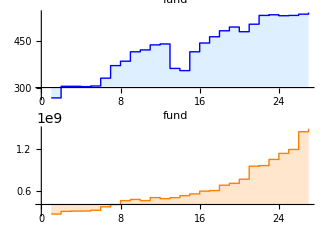
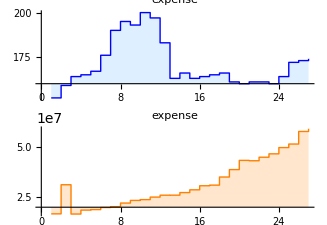
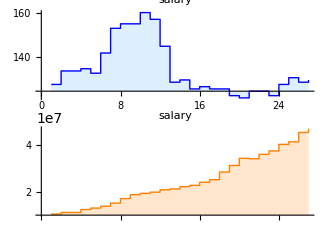
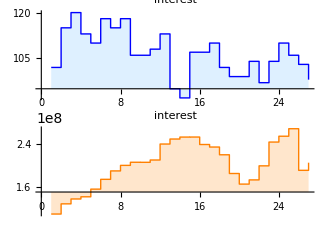
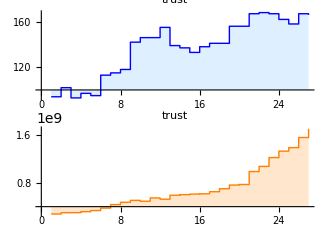
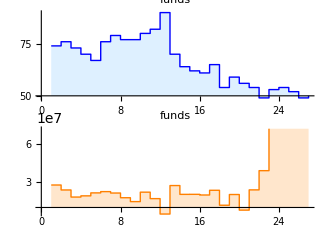
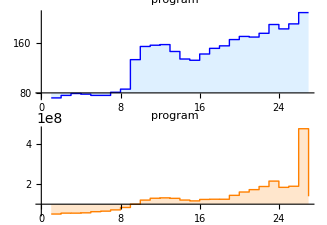
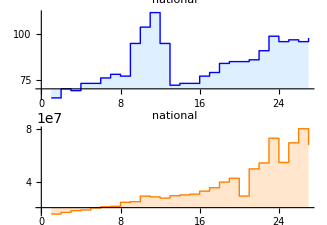

```mathematica
TrendPlot3/@trends[[1;;80]]
```

```mathematica
(* form pdfs and PCA sort the plots
to show similar trends.
(x-min)/(max-min)
*)
```

```mathematica
TrendVec1[trend_]:=Block[{vs,min,max,mean},vs=trend[[2,All,1]];
min=Min[vs]; max=Max[vs];mean=Mean[vs];
If[min==max,ConstantArray[0,Length[vs]],
N[Normalize[(vs-mean)/Max[max-mean,mean-min]]]]
];
TrendVec2[trend_]:=Block[{vs,min,max,mean},vs=trend[[2,All,2]];
min=Min[vs]; max=Max[vs];mean=Mean[vs];
If[min==max,ConstantArray[0,Length[vs]],
N[Normalize[(vs-mean)/Max[max-mean,mean-min]]]]
];
TrendVec3[trend_]:=Join[TrendVec1[trend],TrendVec2[trend]];
```

```mathematica
Needs["MultivariateStatistics`"]
strends=SortBy[Partition[Riffle[trends,PrincipalComponents[TrendVec2/@trends][[All,1]]],2],#[[2]]&][[All,1]];
```

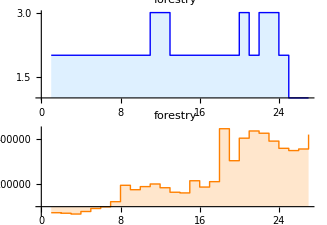
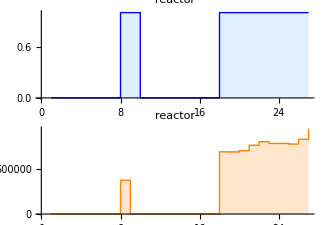
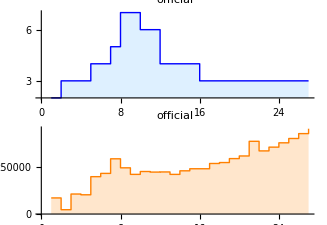
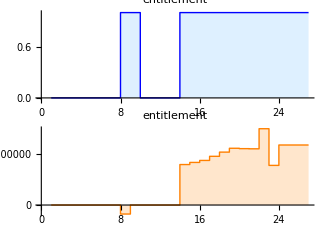
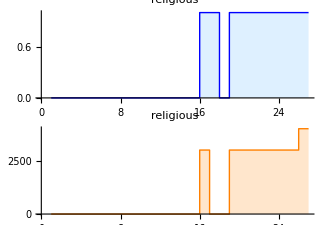
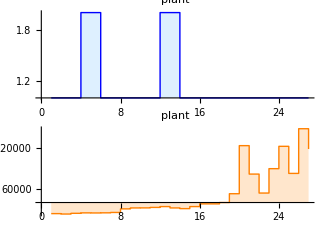
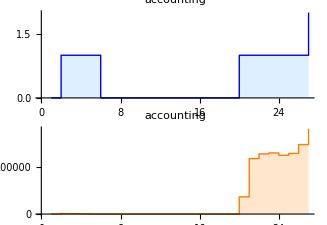
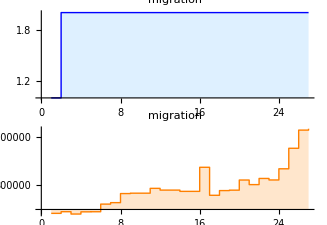
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TrendPlot3/@strends[[200;;250]]
```